### Load packages

```mathematica
<<NFPackages`structuralMechanicsBook` // Quiet;
```

### Assignment 3

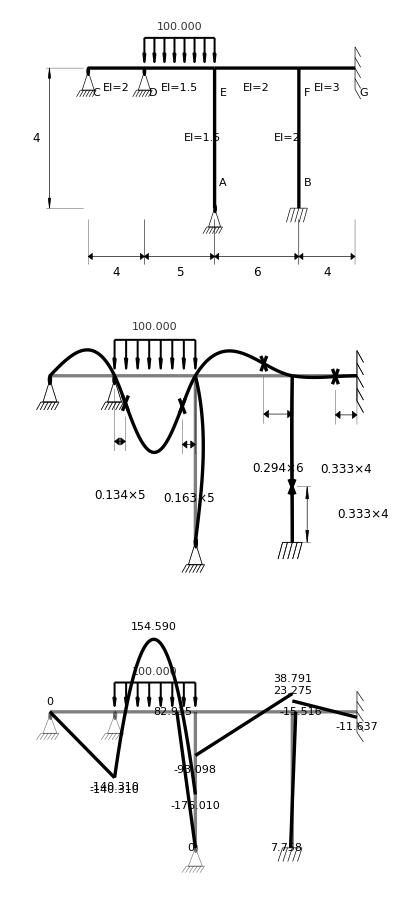

```mathematica
makeBuildingVerticalSpecsAndSolutionGrid[ {4}, {4, 5, 6, 4},600,
buildingBeamUniformLoadList -> { {1, 2} -> 100},
buildingBeamPointForceList -> { },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {{1, 1} -> 2, {1, 2} -> 1.5, {1, 3} -> 2, {1, 4}-> 3},
buildingColumnsEIMagnitudeList -> {{1, 3} -> 1.5, {1, 4}-> 2, _ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> True, {1, 3} -> False, {1, 4}-> False, {1, 5} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {},
buildingSideSupportRightList -> { _ -> "fixed"},
buildingSupportList -> {1 -> "hinge", 2 -> "hinge", 3 -> "hinge", 4 -> "fixed", 5 -> "hinge"},
buildingFactorDisplacement->1 Automatic,
buildingFactorMomentDiagrams -> 0.002,
buildingSolveColumnBeamDisplacementFunctions -> False ]
```